```mathematica
Needs["ErrorBarPlots`"]
ListA={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
ErrorA={.5,.5}
```

{0.5,0.5}

```mathematica
ErrorB={.5,.5}
```

{0.5,0.5}

```mathematica
BestFit=Fit[ListA,{1,x},x]
```

1.+1. x

```mathematica
BestFitPlot=Plot[BestFit,{x,0,4.5}];
```

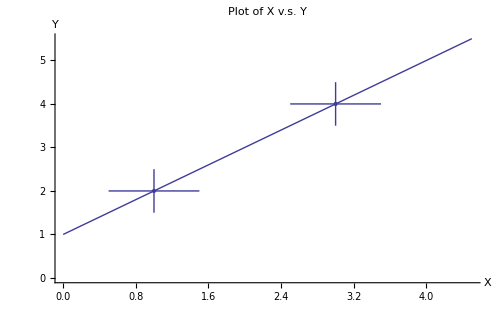

```mathematica
Show[ErrorListPlot[Table[{ListA[[a]],ErrorBar[ErrorA[[a]],ErrorB[[a]]]},{a,1,2}],
AxesLabel->{"X","Y"},
ImageSize->500,PlotLabel->"Plot of X v.s. Y"],BestFitPlot,PlotRange->{{0,4.5},{0,5.5}}]
```